```mathematica
a=−1;b=1;alfa0=1;beta0=0;alfa1=1;beta1=0;gama0=0;gama1=0;
S1=NDSolve[{w''[x]-(1+x^2)w[x]==0,w[-1]==0,w'[-1]==-1},w,{x,-1,1}];
W[x_]=w[x]/.S1;
```

```mathematica
S2=NDSolve[{v''[x]-(1+x^2)v[x]==2x,v[-1]==0,v'[-1]==0},v[x],{x,-1,1}];
V[x_]=v[x]/.S2;
```

```mathematica
dw[x_]=D[w[x],x];dv[x_]=D[v[x],x];
A=(gama1-alfa1*V[b]-beta1*dv[b])/(alfa1*W[b]+beta1*dw[b])
```

{-0.610215}

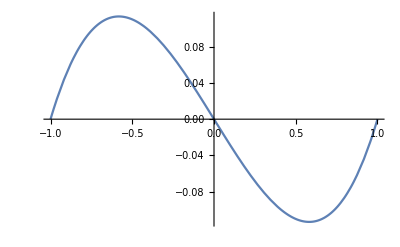

```mathematica
Plot[-0.610215*W[x]+V[x], {x, -1, 1}]
```

```mathematica
FindMaximum[1+x^2, {x, a, b}]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMaximum[1+x^2,{x,a,b}]

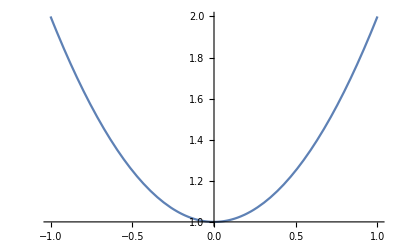

```mathematica
Plot[1+x^2, {x, a,b}]
```

```mathematica
h=0.2;n=10;
```

```mathematica
Array[L, n, 0];Array[M,n,0];Array[u, {n,2},0];
```

```mathematica
u[0,0]=a;u[n,0]=b;u[0,1]=0;u[n,1]=0;L[0]=0;M[0]=0;
```

```mathematica
Do[le=-2-h^2*(1+(a+i*h)^2);bb=1; c=1;d=h^2*2*(a+i*h);L[i]=-c/(bb*L[i-1]+le);M[i]=(d-bb*M[i-1])/(bb*L[i-1]+le), {i, 1, n}];
```

```mathematica
u[n]=M[n];
```

```mathematica
Do[u[n-i,0]=b-i*h;u[n-i,1]=L[n-i]*u[n-i+1,1]+M[n-i],{i,1,n}];
```

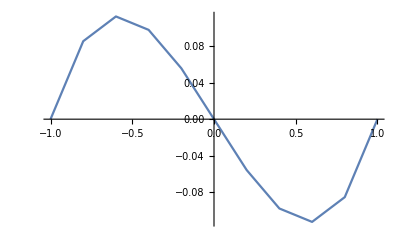

```mathematica
Show[ListPlot[Table[{u[i,0], u[i,1]},{i,0,n}], Joined->True]]
```

```mathematica
s1 = -(alfa1(b-a)^2+beta1*2*(b-a))/(alfa1(b-a)+beta1*1)
```

-2

```mathematica
s2 = -(alfa1(b-a)^2+beta1*3*(b-a))/(alfa1(b-a)+beta1*2)
```

-2

```mathematica
s3 = -(alfa1(b-a)^2+beta1*4*(b-a))/(alfa1(b-a)+beta1*3)
```

-2

```mathematica
s0 =  -(alfa1(b-a)^2+beta1*(b-a))/(alfa1(b-a))
```

-2

```mathematica
f0 = s0*1+(t-a)^1
```

-1+t

```mathematica
f0 =Expand[f0]
```

-1+t

```mathematica
f1 = Expand[s1*(t-a)+(t-a)^2]
```

-1+t^2

```mathematica
f2 = Expand[s1*(t-a)^2+(t-a)^3]
```

-1-t+t^2+t^3

```mathematica
f3 = Expand[s1*(t-a)^3+(t-a)^4]
```

-1-2 t+2 t^3+t^4

```mathematica
U=f0+c1*f1+c2*f2+c3*f3
```

-1+t+c1 (-1+t^2)+c2 (-1-t+t^2+t^3)+c3 (-1-2 t+2 t^3+t^4)

```mathematica
r = 2*t-U
```

1+t-c1 (-1+t^2)-c2 (-1-t+t^2+t^3)-c3 (-1-2 t+2 t^3+t^4)

```mathematica
t = -0.1245
```

-0.1245

```mathematica
r
```

```mathematica
eq1 =0.8755+0.98449975 c1+0.8619295311249999 c2+0.7546193044999375 c3==0
```

0.8755+0.9845 c1+0.86193 c2+0.754619 c3==0

```mathematica
t = 0.6754
```

0.6754

```mathematica
r
```

```mathematica
eq2 =1.6754+0.5438348399999999 c1+0.9111408909359999 c2+1.5265254486741744 c3==0
```

1.6754+0.543835 c1+0.911141 c2+1.52653 c3==0

```mathematica
t = 0.8439
```

0.8439

```mathematica
r
```

```mathematica
eq3=1.8439+0.28783279000000006 c1+0.5307348814810002 c2+0.9786220479628165 c3==0
```

1.8439+0.287833 c1+0.530735 c2+0.978622 c3==0

```mathematica
result = Solve[{eq1, eq2, eq3}, {c1,c2,c3}]
```

{{c1→-24.234,c2→42.0299,c3→-17.5505}}

```mathematica
Clear[t]
```

```mathematica
Ufinal= f0-24.234011685499247*f1+42.02990139761773*f2-17.550484966434666*f3
```

-1+t-24.234 (-1+t^2)+42.0299 (-1-t+t^2+t^3)-17.5505 (-1-2 t+2 t^3+t^4)

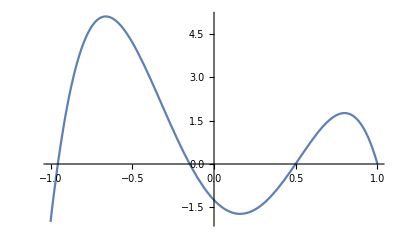

```mathematica
Plot[Ufinal, {t,-1,1}]
```

```mathematica
Clear[t]
```

```mathematica
Clear[y]
```

```mathematica
OriginalSolve = NDSolve[{y''[t]-(1+t^2)*y[t]==2*t, y[-1]==0, y[1]==0},y[t],{t,a,b}]
```

{{y[t]→InterpolatingFunction[…][t]}}

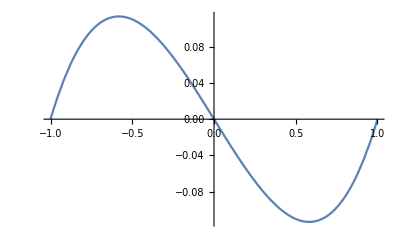

```mathematica
Plot[Evaluate[y[t]/.OriginalSolve], {t, a, b}, PlotRange->All]
```

```mathematica
Clear[f0,f1,f2, U]
```

```mathematica
f0[x_]=1+x^1;
f1[x_]=1+2x^2;
```

```mathematica
f2[x_]=1+8x^3;
```

```mathematica
U[x_, c1_,c2_]=f0[x]+c1*f1[x]+c2*f2[x];
```

```mathematica
R[x_]=2*x-U[x, c1, c2];
```

```mathematica
S = Solve[{Integrate[R[x]*f1[x],{x,-1,1}]==0,
Integrate[R[x]*f2[x],{x,-1,1}]==0}, {c1,c2}]
```

{{c1→-705/1142,c2→917/5710}}

```mathematica
Ufinal=f0[x]+N[-705/1142]*f1[x]+N[917/5710]*f2[x];
```

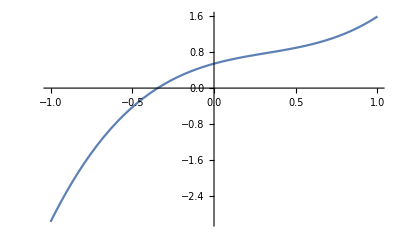

```mathematica
Plot[Ufinal, {x,-1,1}]
```

```mathematica
Clear[x,a];
n=4;Array[a,{n-1,n-1}];Array[b,n-1];
Array[x,n+1,0];x[0]=-1;x[n]=1;h=0.5;
Do[x[i]=x[0]+i*h,{i,1,n}];p[x_]:=0;q[x_]:=-1(1+x^2);
M1[l_]:=Integrate[-1+p[x](x-x[l-1])+q[x](x-x[l-1])^2,{x,x[l-1],x[l]}]/h/h;
M2[l_]:=Integrate[-1+p[x](x-x[l+1])+q[x](x-x[l+1])^2,{x,x[l],x[l+1]}]/h/h;
H[l_]:=Integrate[1-p[x](x-x[l+1])-q[x](x-x[l+1])*(x-x[l]),{x,x[l],x[l+1]}]/h/h;
```

```mathematica
L[l_]:=Integrate[1-p[x](x-x[l-1])-q[x](x-x[l-1])*(x-x[l]),{x,x[l-1],x[l]}]/h/h;
```

```mathematica
Do[Do[If[Abs[(i-k)]>1, a[i,k]=0];If[i==k,a[i,k]=N[M1[i]+M2[i]]];If[i==k-1,a[i,k]=N[H[i]]];If[i==k+1,a[i,k]=N[L[i]]], 
{i, 1,n-1}], {k, 1, n-1}]
```

```mathematica
MatrixForm[A=Array[a, {n-1,n-1}]]
```

(-4.425 | 1.91042 | 0
0.636829 | -4.34167 | 1.91042
0 | 0.709436 | -4.425)

```mathematica
v[x]''-(1+x^2)*v[x]==F[x];
```

```mathematica
F[x]:=2x;
```

```mathematica
Do[bi[i]=1/h*(Integrate[F[x]*(x-x[i-1]), {x, x[i-1], x[i]}]-Integrate[F[x]*(x-x[i+1]),{x, x[i],x[i+1]}]),{i, 1,n-1}]
```

```mathematica
B=Array[bi, n-1]
```

{-0.5,0.,0.5}

```mathematica
V = LinearSolve[A,B]
```

{0.0964724,-0.038269,-0.11913}

```mathematica
Clear[u]
```

```mathematica
Array[u,{n+1,2},{0,0}];
```

```mathematica
u[0,0]=-1;
```

```mathematica
u[n, 0]=1;
u[0,1]=0;
u[n,1]=0;
```

```mathematica
Do[u[i,0]=x[i];u[i,1]=V[[i]], {i,1,n-1}];
```

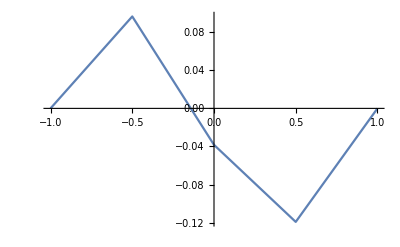

```mathematica
Show[ListPlot[Table[{u[i,0],u[i,1]},{i,0,n+1}], Joined->True]]
```

```mathematica
Show[P;ListPlot[Table[{u[i,0],u[i,1]},{i,0,n+1}], Joined->True]]
```